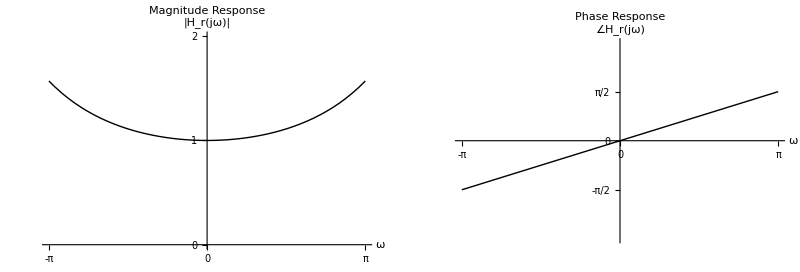

```mathematica
(*定义参数*)T=1;
ωs=(2 π)/T;

(*定义传递函数 Hr*)
Hr[ω_]:=(ω*Exp[I*ω*T/2])/(2*Sin[ω*T/2])

(*1. 绘制幅度谱|Hr(jω)|*)
magnitudePlot=Plot[Abs[Hr[ω]],{ω,-ωs/2,ωs/2},PlotRange->{{-π,π},{0,2}},Exclusions->{0},(*排除分母为0的点，虽然极限存在*)PlotStyle->{Black,Thick},AxesLabel->{"ω","|H_r(jω)|"},PlotLabel->"Magnitude Response",Ticks->{{-π,0,π},{0,1,2}},GridLines->Automatic];

(*2. 绘制相位谱 Arg(Hr(jω))*)
phasePlot=Plot[Arg[Hr[ω]],{ω,-ωs/2,ωs/2},PlotRange->{{-π,π},{-π,π}},PlotStyle->{Black,Thick},AxesLabel->{"ω","∠H_r(jω)"},PlotLabel->"Phase Response",Ticks->{{-π,0,π},{-π/2,0,π/2}},GridLines->Automatic];

(*同时显示两张图*)
GraphicsGrid[{{magnitudePlot,phasePlot}},ImageSize->800]
```